```mathematica
Clear[x, y, nx, ny]
Integrate[E^(ⅈ*(nx*x + 2*m*(Cos[nx]))), {nx, 0, 2π}]
Integrate[E^(ⅈ*(nx*x + ny*y + 2*m*(Cos[nx] + Cos[ny]))), {nx, 0, 2π}, {ny, 0, 2π}]
```

∫_0^(2 π) ⅇ^(ⅈ (nx x+2 m Cos[nx]))ⅆnx

∫_0^(2 π) ∫_0^(2 π) ⅇ^(ⅈ (nx x+ny y+2 m (Cos[nx]+Cos[ny])))ⅆnyⅆnx

```mathematica
M = 21;
ϕ[x_, y_, t_] := NSum[E^(ⅈ*((2*π/M)*nx*x + (2*π/M)*ny*y + 2*(Cos[(2*π/M)*nx] + Cos[(2*π/M)*ny] + Cos[(2*π/M)*(nx + ny)])*t)), {nx, 0, M - 1}, {ny, 0, M - 1}]/M^2

dataHex = Table[Table[ϕ[x, y, τ] // Chop, {x, -10, 10}, {y, -10, 10}], {τ, 0, 10, .5}];
```

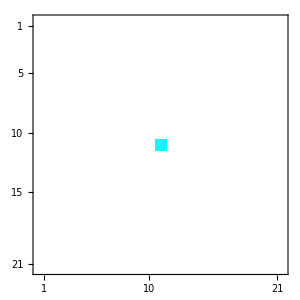
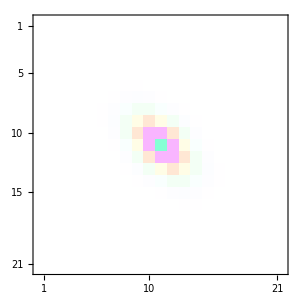
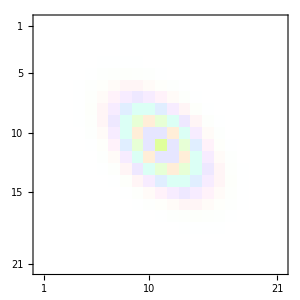
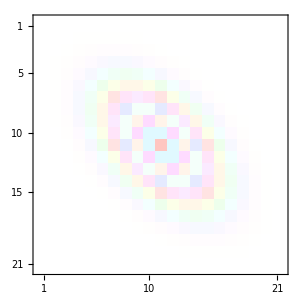
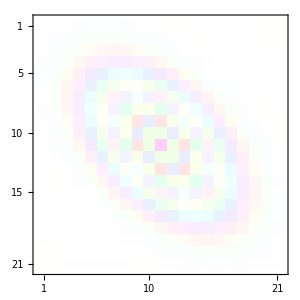
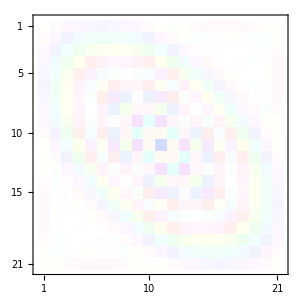
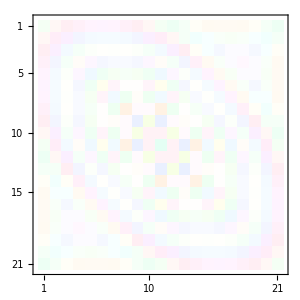
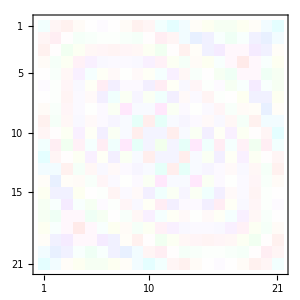

```mathematica
SeedRandom[1]
a={{0,.1, 1, 5, 10, 20, 100}, {0,.1, 1, 5, 10, 20, 100}*(1 + ⅈ), {0,.1, 1, 5, 10, 20, 100}*ⅈ, Table[E^(ⅈ*x), {x, 0, 3, .5}]};

Clear[mp]
mp[a_]:=MatrixPlot[Hue[(Arg[#]+Pi)/2/Pi, Abs@#]&/@#&/@a,ImageSize->300];
Row[Table[mp[d], {d, dataHex}]]
```